```mathematica
ga10k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gaptest/l1e4-all3.txt",{Number,Number}];
ga20k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gaptest/l2e4-all2.txt",{Number,Number}];
ga30k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gaptest/l3e4-all2.txt",{Number,Number}];
ga40k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gaptest/l4e4-all.txt",{Number,Number}];
ga50k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gaptest/l5e4-all2.txt",{Number,Number}];
ga100k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gaptest/l10e4-all2.txt",{Number,Number}];
```

```mathematica
ga10k1=ga10k[[All,1]];
ga20k1=ga20k[[All,1]];
ga30k1=ga40k[[All,1]];
ga50k1=ga50k[[All,1]];
ga100k1=ga100k[[All,1]];
ga10k2=ga10k[[All,2]];
ga20k2=ga20k[[All,2]];
ga30k2=ga40k[[All,2]];
ga50k2=ga50k[[All,2]];
ga100k2=ga100k[[All,2]];
```

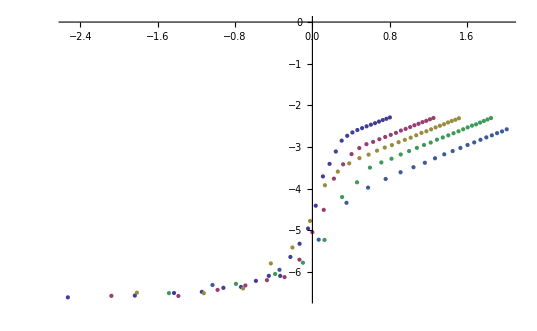

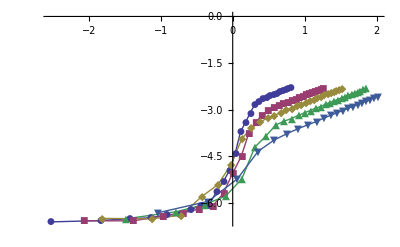

```mathematica
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.0;

ga10k1=ga10k[[All,1]];
ga20k1=ga20k[[All,1]];
ga30k1=ga40k[[All,1]];
ga50k1=ga50k[[All,1]];
ga100k1=ga100k[[All,1]];
ga10k2=ga10k[[All,2]];
ga20k2=ga20k[[All,2]];
ga30k2=ga40k[[All,2]];
ga50k2=ga50k[[All,2]];
ga100k2=ga100k[[All,2]];

g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,1,Length[ga10k1]}];

g20k=Table[{Log[ga20k1[[i]]-d0]+z*Log[20*1000.],Log[ga20k2[[i]]]+α*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0]+z*Log[30*1000.],Log[ga30k2[[i]]]+α*Log[30*1000.]},{i,1,Length[ga30k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,1,Length[ga50k1]}];
g100k=Table[{Log[ga100k1[[i]]-d0]+z*Log[100*1000.],Log[ga100k2[[i]]]+α*Log[100*1000.]},{i,1,Length[ga100k1]}];
ListPlot[{g10k,g20k,g30k,g50k,g100k},PlotRange->Full]
ListPlot[{g10k,g20k,g30k,g50k,g100k},PlotLegend->{"10k","20k","30k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic]
```

```mathematica
;
```

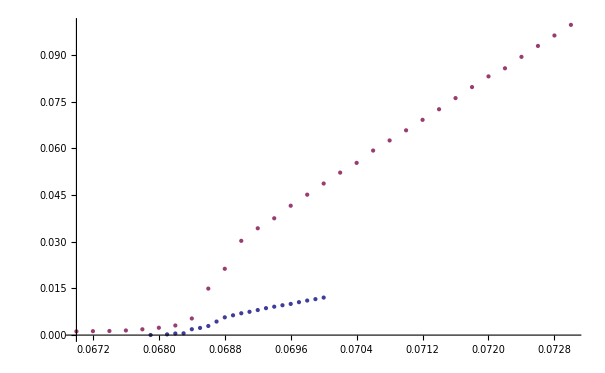

```mathematica
ListPlot[{gap50k,ga50k}]
```

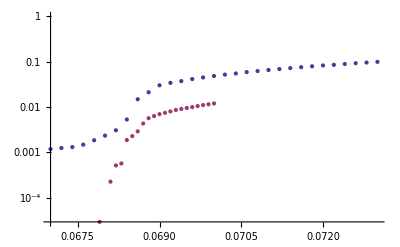

```mathematica
ListLogPlot[{ga100k,gap100k}]
```

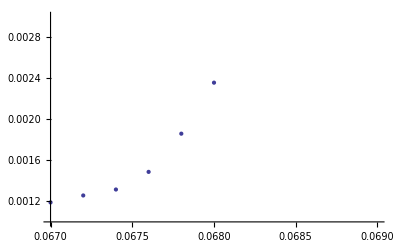

```mathematica
ListPlot[{ga50k},PlotRange->{{0.067,0.069},{0.001,0.003}}]
```

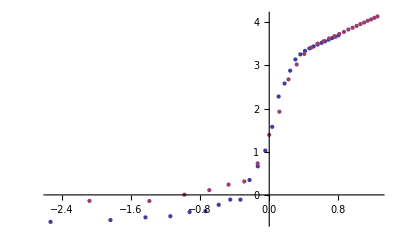

```mathematica
ListPlot[{g10k,g20k}]
```

```mathematica
ta10k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/gap3/timeevolution.d.0.069.l2e4-all.txt",{Number,Number}];
```

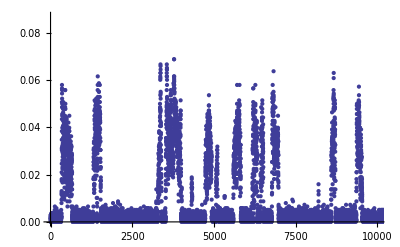

```mathematica
ListPlot[ta10k,PlotRange->{{0,10000},Full}]
```

```mathematica
gap20k
```

{{0.0685,0.0000961241},{0.06875,0.000253924},{0.069,0.00098513},{0.06925,0.00272399},{0.0695,0.00541373},{0.06975,0.00864103},{0.07,0.0106991},{0.07025,0.0120417},{0.0705,0.0135375},{0.07075,0.0146914},{0.071,0.0156374},{0.07125,0.0168185},{0.0715,0.0179363},{0.07175,0.0193039},{0.072,0.0205148}}